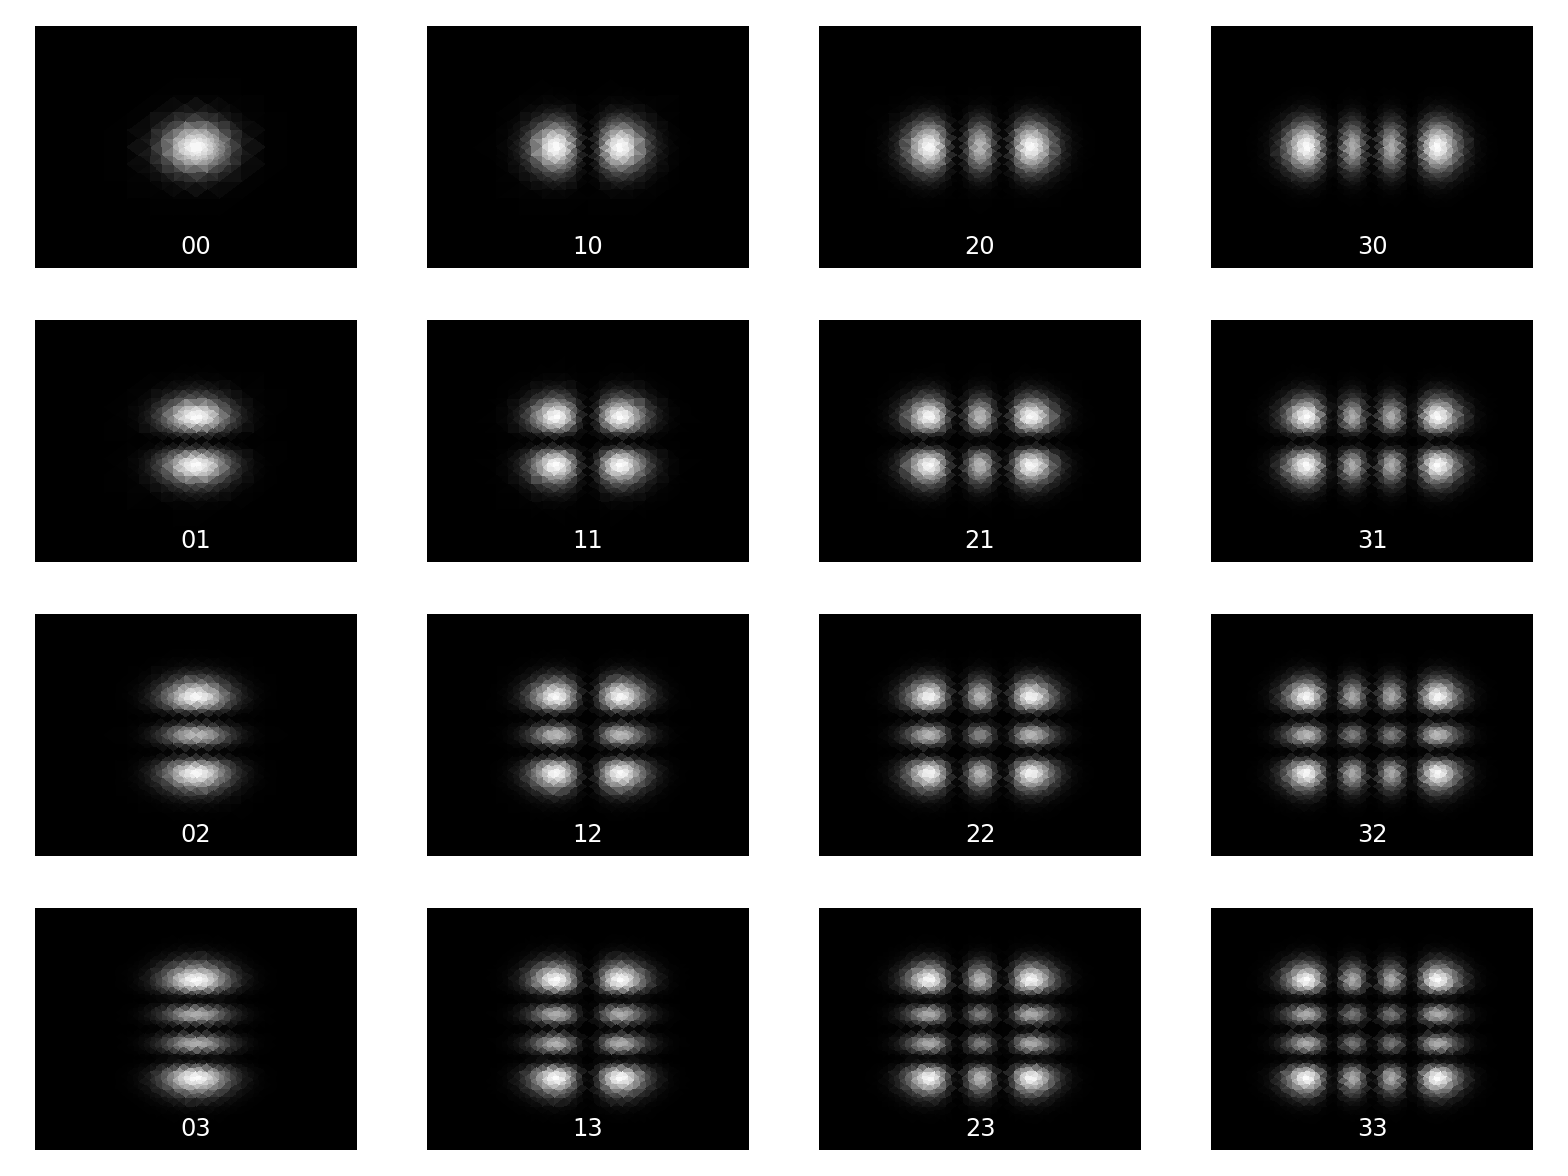

```mathematica
(*Define a function for the intensity of each TEMmn mode*)
Imn[x_,y_,m_,n_]:=(HermiteH[m,x] Exp[-x^2/2])^2 (HermiteH[n,y] Exp[-y^2/2])^2

(*Plot the intensity for different m and n values*)
opts=Sequence[PlotRange->All,ColorFunction->GrayLevel,Frame->False,PlotRangePadding->None];
TableForm[Table[DensityPlot[Imn[x,y,m,n],{x,-5,5},{y,-5,5},Evaluate@opts,Epilog->Text[Style[StringJoin[ToString/@{m,n}],24,White],Scaled[{0.5,0.1}]]],{n,0,3},{m,0,3}],TableSpacing->{0,0}]
```

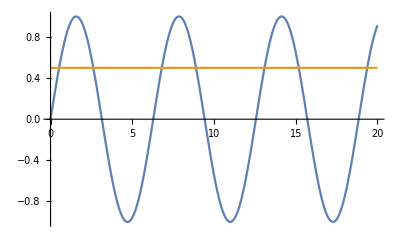

```mathematica
Plot[{Sin[x] ,1/2 },{x,0,20}]
```

```mathematica
ContourPlot[Cos[x^2]+Cos[y^2],{x,0,4Pi},{y,0,4Pi},PlotLegends->"Expressions"]
```

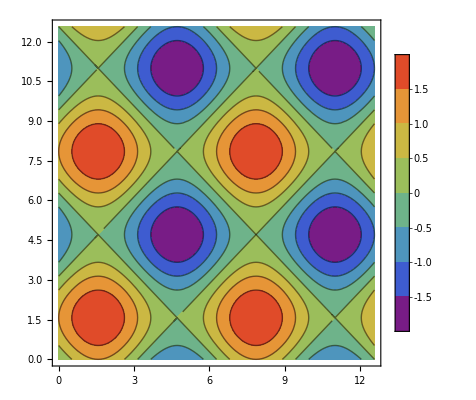

```mathematica
ContourPlot[Sin [x]+Sin[y],{x,0,4Pi},{y,0,4Pi},PlotLegends->Automatic, ColorFunction->"Rainbow"]
```